```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/saul/sauld@cimat.mx/UNISON/Articles/PicewiseOC-ARC-Submition/NovelCovid19-OptimalPiecewiseControlModelling/Covid19Paper/test/runDec25_2020

```mathematica
FNames=FileNames["*.dat"];
Fk[k_]:=Import[FNames[[k]]];
FNames
FNames[[1]]
```

{best.dat,ControlClases.dat,datos_180_720_3000.dat,NoControlClases.dat,rvecs_180_720_3000.dat}

best.dat

```mathematica
AmatC = Fk[2];
ControlSignals = Fk[3];
AmatNC = Fk[4];
Dimensions[AmatC];
Dimensions[AmatNC];
Dimensions[ControlSignals];
tvecC = AmatC[[All,1]];
tvecNC = AmatNC[[All,1]];
tU =ControlSignals[[All, 1]];
xclases={"time","L","S","E","I_S","I_A","H","R","D","V","Vcon"};
dim=Length[xclases];
OvDyn = Prepend[AmatC, xclases];
vDyn = Prepend[AmatNC, xclases];
Export["ovpEff95Cov20T360.csv",OvDyn,"csv"];
Export["vpEff95Cov20T360.csv",vDyn,"csv"];
```

## Uncontrolled dynamics data generation

```mathematica
ClearAll;
```

```mathematica
prm=Association[Import["vaccination_parameters.json", "JSON"]];
Nstar [l_,s_,e_,is_,ia_,h_,r_]:=l + s + e + is + ia +h + r ;
InfectionForce[l_,s_,e_,is_,ia_,h_,r_]:=
(prm["beta_s"]*is+prm["beta_a"]*ia)/Nstar[l, s, e,is,ia, h, r];
TableForm[prm]
```

<|beta_s→0.363282,beta_a→0.251521,epsilon→0.95,var_epsilon→0.1,kappa→0.196078,delta_l→0.0333333,delta_h→0.2,delta_v→0.00273973,delta_r→0.00555556,p→0.1213,theta→0.2,gamma_a→0.167504,gamma_s→0.0925069,gamma_h→0.507987,mu→0.0000391389,mu_i_s→0.,mu_h→0.01632,lambda_v→0.000611352,lambda_t→0.00047895,a_E→0.00841847,a_D→7.25,a_V→1.,c_V→1.,c_T→0.,h_max→9500.,d_final→0.01,coverage→0.2,hospitalization_rate→0.05,d_max→0.000051928,n_pop→2.64464×10^7,T→365,L_0→0.26626,S_0→0.463606,E_0→0.00067033,I_S_0→0.00009283,I_A_0→0.00120986,H_0→0.000134158,R_0→0.266126,D_0→0.00190074,V_0→0.,X_0→0.,X_f→0.2,Y_inc_0→0.122582|>

```mathematica
NCSol = 
NDSolve[
{
l'[t]== prm["theta"] * prm["mu"] * Nstar[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]] - (prm["var_epsilon"] * InfectionForce[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]] +prm["delta_l"]+prm["mu"])*l[t],
s'[t]==(1.0-prm["theta"])*prm["mu"]*Nstar[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]]+prm["delta_l"] * l[t] + prm["delta_r"] * rr[t]-(InfectionForce[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]]+prm["mu"])* s[t],
e'[t]==InfectionForce[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]]*(prm["var_epsilon"]*l[t]+s[t])-(prm["kappa"]+prm["mu"])*e[t],
is'[t]==prm["p"] * prm["kappa"]* e[t]-(prm["gamma_s"]+prm["delta_h"]+prm["mu"])*is[t],
ia'[t]==(1.0-prm["p"])*prm["kappa"]*e[t]-(prm["gamma_a"]+prm["mu"])*ia[t],
h'[t]==prm["delta_h"]*is[t]-(prm["gamma_h"] + prm["mu_h"] + prm["mu"]) * h[t],
rr'[t]==prm["gamma_s"]*is[t] + prm["gamma_a"] * ia[t] + prm["gamma_h"] * h[t]-(prm["delta_r"] + prm["mu"]) * rr[t],
dd'[t]==prm["mu_h"] * h[t],
l[0]==prm["L_0"],
s[0]==prm["S_0"],
e[0]==prm["E_0"],
is[0]==prm["I_S_0"],
ia[0]==prm["I_A_0"],
h[0]==prm["H_0"],
rr[0]==prm["R_0"],
dd[0]==prm["D_0"]
},
{l, s, e, is, ia, h,rr,dd},
{t, 0, 360}
];
DataHeader={"time","L","S","E","I_S","I_A","H","R","D"};
```

```mathematica
dataNoVacinationSol = Table[
Flatten[
{
t,
Evaluate[{l[t]}/.NCSol],
Evaluate[{s[t]}/.NCSol],
Evaluate[{e[t]}/.NCSol],
Evaluate[{is[t]}/.NCSol],
Evaluate[{ia[t]}/.NCSol],
Evaluate[{h[t]}/.NCSol],
Evaluate[{rr[t]}/.NCSol],
Evaluate[{dd[t]}/.NCSol],
}
],
{t,0,360,0.1}];
cl = Table[
Flatten[
{
t,
Evaluate[{l[t]}/.NCSol] +
Evaluate[{s[t]}/.NCSol] +
Evaluate[{e[t]}/.NCSol] +
Evaluate[{is[t]}/.NCSol] +
Evaluate[{ia[t]}/.NCSol] +
Evaluate[{h[t]}/.NCSol] +
Evaluate[{rr[t]}/.NCSol] +
Evaluate[{dd[t]}/.NCSol]
}
],
{t,0,360,0.1}];
dataNoVacinationSol = Prepend[dataNoVacinationSol, DataHeader];
Export["dataNoVacinationSo.csv", dataNoVacinationSol];
```

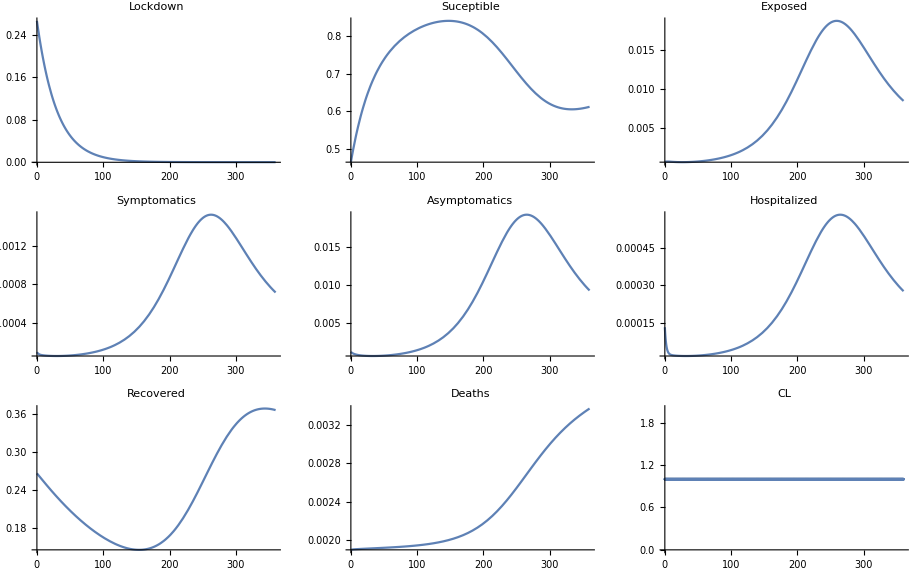

```mathematica
pltNVL=Plot[
Evaluate[l[t]/.NCSol],
{t,0,360},
PlotRange->All,
PlotLabel->"Lockdown"
];
pltNVS=Plot[
Evaluate[s[t]/.NCSol],
{t,0,360},
PlotRange->All,
PlotLabel->"Suceptible"
];
pltNVE=Plot[
Evaluate[e[t]/.NCSol],
{t,0,360},
PlotRange->All,
PlotLabel->"Exposed"
];
pltNVIS=Plot[
Evaluate[is[t]/.NCSol],
{t,0,360},
PlotRange->All,
PlotLabel->"Symptomatics"
];

pltNVIA=Plot[
Evaluate[ia[t]/.NCSol],
{t,0,360},
PlotRange->All,
PlotLabel->"Asymptomatics"
];
pltNVH=Plot[
Evaluate[h[t]/.NCSol],
{t,0,360},
PlotRange->All,
PlotLabel->"Hospitalized"
];
pltNVR=Plot[
Evaluate[rr[t]/.NCSol],
{t,0,360},
PlotRange->All,
PlotLabel->"Recovered"
];
pltNVD=Plot[
Evaluate[dd[t]/.NCSol],
{t,0,360},
PlotRange->All,
PlotLabel->"Deaths"
];
pltCL=ListPlot[
Thread[{cl[[All,1]], cl[[All,2 ]]}],
PlotRange->All,
PlotLabel->"CL"
];

outplot = GraphicsGrid[
{
{pltNVL, pltNVS, pltNVE}, 
{pltNVIS, pltNVIA, pltNVH},
{ pltNVR, pltNVD, pltCL}
}
]
```

Optimal and no optimal controlled dynamics

```mathematica
plotdatC[k_]:= 
ListStepPlot[
Thread[{tvecC,AmatC[[All,k+1]]}],
PlotStyle->{Thick,Blue},
AxesLabel->{"t",xclases[[k]]}
];
plotdatNC[k_]:=
ListStepPlot[
Thread[{tvecNC,AmatNC[[All,k+1]]}],
PlotStyle->{Thick,Red},AxesLabel->{"t",xclases[[k]]},
PlotRange->All];
```

```mathematica
PlotTime=tvecC; 
L = AmatC[[All,2]]; S = AmatC[[All,3]]; Ex = AmatC[[All,4]];
IS =AmatC[[All,5]]; IA = AmatC[[All,6]]; H= AmatC[[All,7]]; 
R = AmatC[[All,8]]; Dcov = AmatC[[All,9]];  V= AmatC[[All,10]];
Xcov = AmatC[[All,11]];
nL = AmatNC[[All,2]]; nS = AmatNC[[All,3]]; nEx = AmatNC[[All,4]];
nIS =AmatNC[[All,5]]; nIA = AmatNC[[All,6]]; nH= AmatNC[[All,7]]; 
nR = AmatNC[[All,8]]; nDcov = AmatNC[[All,9]]; nV= AmatNC[[All,10]];
nXcov = AmatNC[[All,11]];
tControl=ControlSignals[[All,1]]; 
uL=0.002777777777777778 + ControlSignals[[All,2]];
uV=0.0006113521953813965+ControlSignals[[All,3]];
doses = 100000 * uV * (L + S + E + IA + R);
```

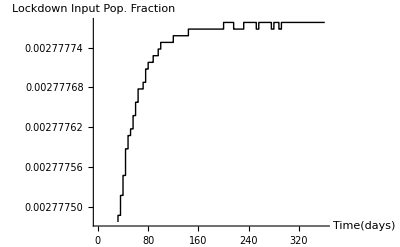

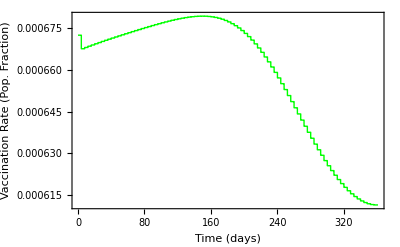

```mathematica
pltuL= 
ListStepPlot[
Thread[{tControl, uL}],
PlotStyle->{Thick,Black},
AxesLabel->{"Time(days)", "Lockdown Input Pop. Fraction"}
(*PlotRange->All*)
]
pltuV= 
ListStepPlot[
Thread[{tControl, uV}],
PlotStyle->{Thick,Green},
(*AxesLabel->{"Time(days)", "Vaccination Rate Modulation"},*)
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Vaccination Rate (Pop. Fraction)",None},
{"Time (days)", None}},
	FrameTicks->All
(*PlotRange->All*)
]
pltuDoses= 
ListStepPlot[
Thread[{tControl, doses}],
PlotStyle->{Thick,Gray},
(*AxesLabel->{"Time(days)", "Doses per 100000 inhabitants"},*)
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Doses per 100000 inhabitants)",None},
{"Time (days)", None}},
	FrameTicks->All
(*PlotRange->All*)
];
```

```mathematica
(*TODO: implement coverage*)
```

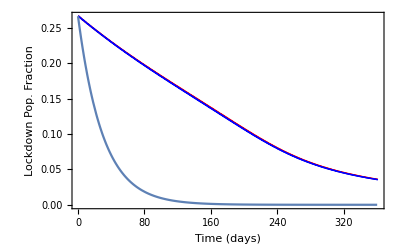

```mathematica
pltnL =
ListStepPlot[
Thread[{tvecNC,nL}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Lockdown Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Lockdown Pop. Fraction",None},
{"Time (days)", None}},
	FrameTicks->All
(*PlotRange->{{0,365}, {0.0, 0.6}}*)
];
pltL =
ListStepPlot[
Thread[{tvecC,L}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Lockdown Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Suceptible (Pop. Fraction)",None},
{"Time (days)", None}},
	FrameTicks->All
];
Show[pltnL, pltL, pltNVL]
```

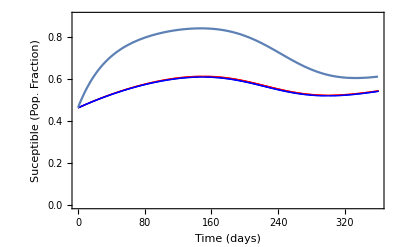

```mathematica
pltnS =
ListStepPlot[
Thread[{tvecNC,nS}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Suceptible Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Suceptible (Pop. Fraction)",None},
{"Time (days)", None}},
	FrameTicks->All,
PlotRange->{{0,360}, {0.0, 0.9}}
];
pltS =
ListStepPlot[
Thread[{tvecC,S}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Suceptible Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Suceptible (Pop. Fraction)",None},
{"Time (days)", None}},
	FrameTicks->All
];
Show[pltnS, pltS,pltNVS]
```

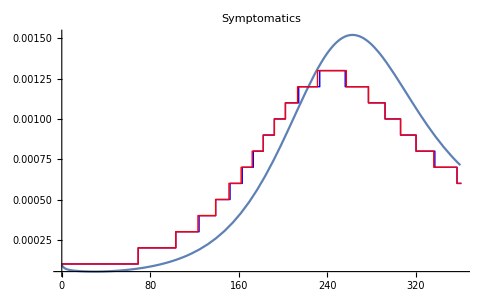

```mathematica
pltnIS =
ListStepPlot[
Thread[{tvecNC,nIS}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Symptomatic Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Symptomatic (Pop. Fraction)",None},
{"Time (days)", None}},
	FrameTicks->All
];
pltIS =
ListStepPlot[
Thread[{tvecC,IS}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Symptomatic Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Symptomatic (Pop. Fraction)",None},
{"Time (days)", None}},
	FrameTicks->All
];
Show[pltNVIS, pltIS, pltnIS]
```

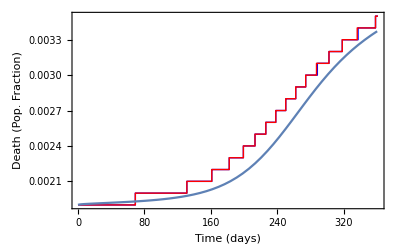

```mathematica
pltnD =
ListStepPlot[
Thread[{tvecNC,nDcov}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Death Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Death (Pop. Fraction)",None},
{"Time (days)", None}},
	FrameTicks->All
];
pltD =
ListStepPlot[
Thread[{tvecC,Dcov}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Death Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Death (Pop. Fraction)",None},
{"Time (days)", None}},
	FrameTicks->All
];
Show[pltD, pltnD, pltNVD]
```

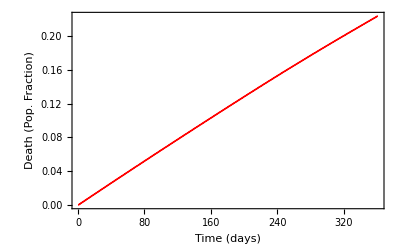

```mathematica
pltnVc =
ListStepPlot[
Thread[{tvecNC, Xcov}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Death Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Death (Pop. Fraction)",None},
{"Time (days)", None}},
	FrameTicks->All
]
```

Coverage

Here we implement the cumulative quadrature of

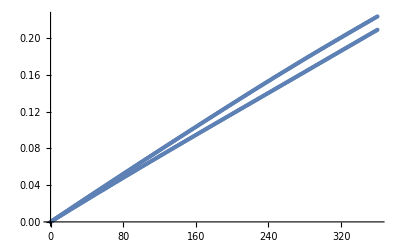

```mathematica
ToExpression[
"x_{vac}(t) = \\int_{0}^{t} (\\lambda_{V} + u_V)(L + S + EE + A + R) \\, dx",
TeXForm, HoldForm];
doseT = Interpolation[
Thread[{tControl,0.0006113521953813965 * (L + S + E + IA + R)}]
];
ControlledDoseT = Interpolation[
Thread[{tControl,uV * (L + S + E + IA + R)}]
];
xCov[t_]:=NIntegrate[doseT[s],{s,0, t}];
ControlledxCov[t_]:=NIntegrate[ControlledDoseT [s],{s,0, t}];
p1 = Plot[xCov[t], {t, 0, 360}];
p2 = Plot[ControlledxCov[t], {t, 0, 360}];
pp1 = ListPlot[Thread[{tControl, Xcov}]];
pp2 = ListPlot[Thread[{tControl, nXcov}]];
Show[pp1,pp2]
```

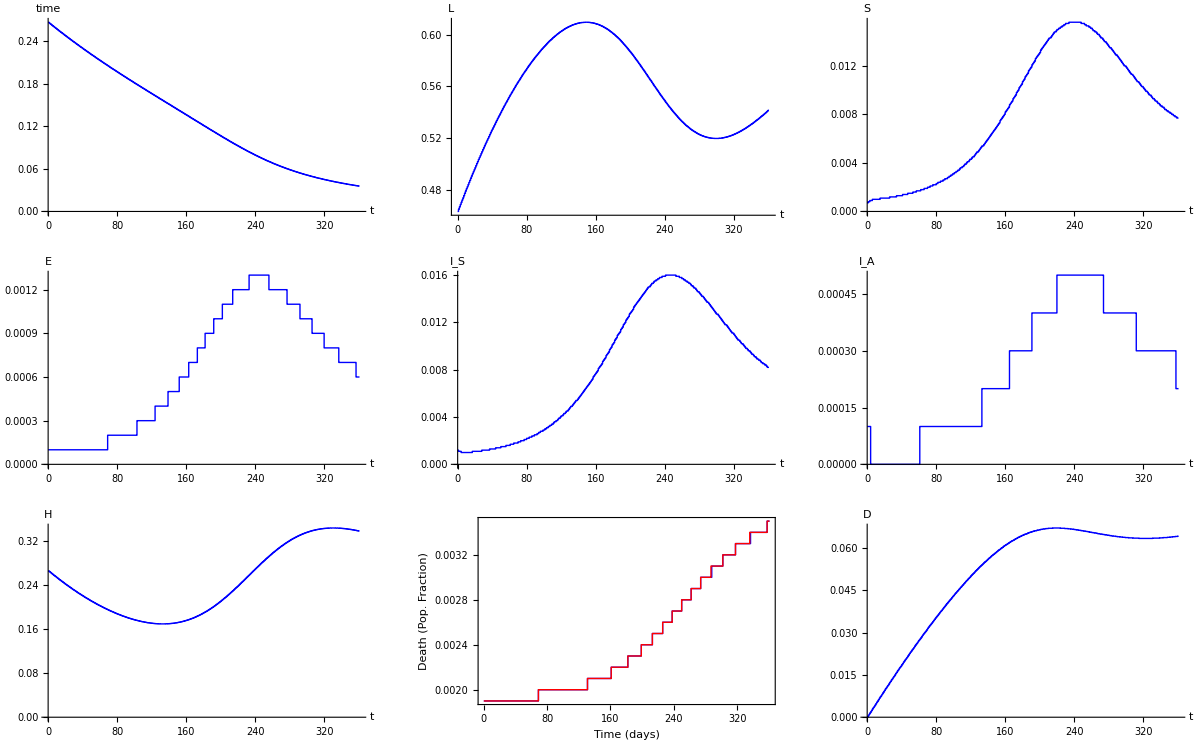

```mathematica
(*Controlled dynamics*)
GraphicsGrid[
{
{plotdatC[1],plotdatC[2], plotdatC[3]},
{plotdatC[4],plotdatC[5], plotdatC[6]},
{plotdatC[7],Show[pltD, pltnD], plotdatC[9]}
}
]
```

```mathematica
Her we need to run the dynamics without vaccination
```

dynamics Her need run the to vaccination we without

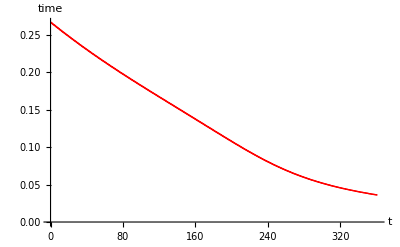
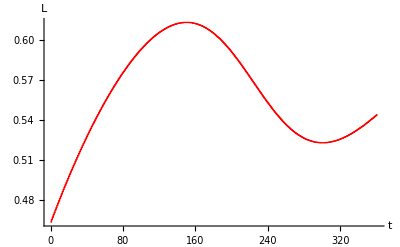
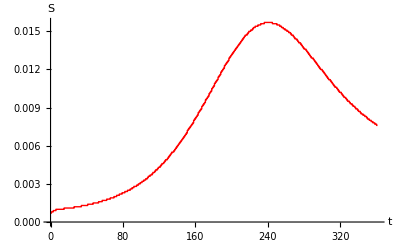
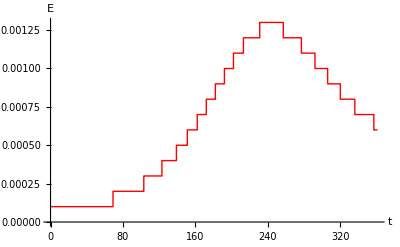
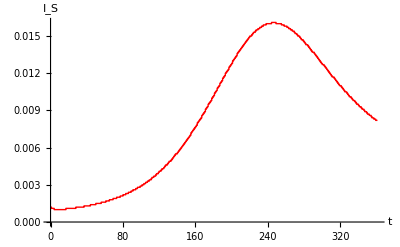
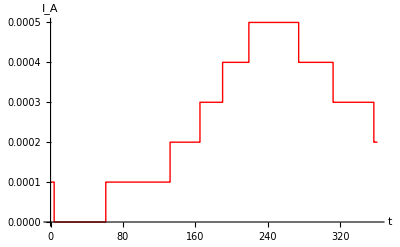
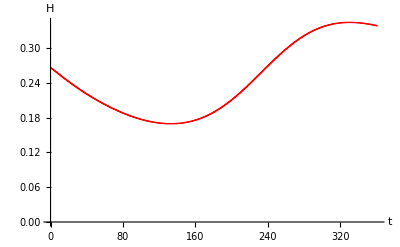
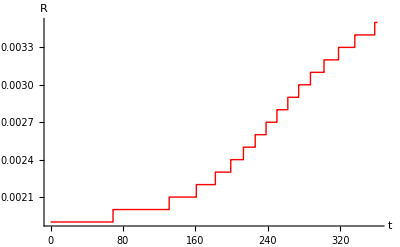

```mathematica
(*Clases NO optimized*)
Table[plotdatNC[k],{k,1,dim-1}]
```

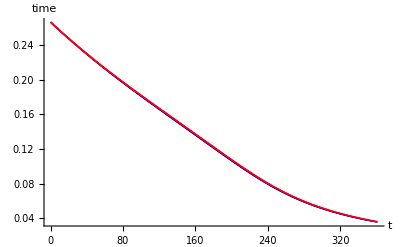
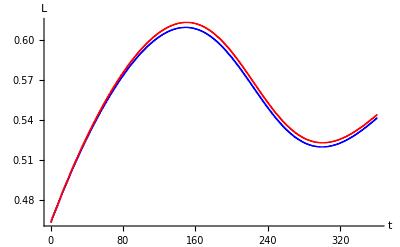
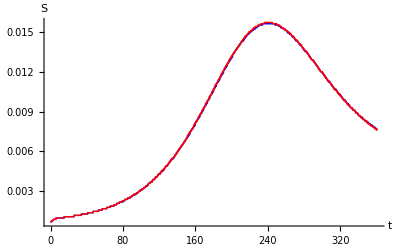
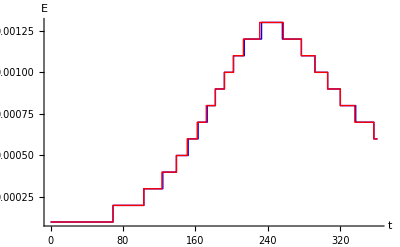
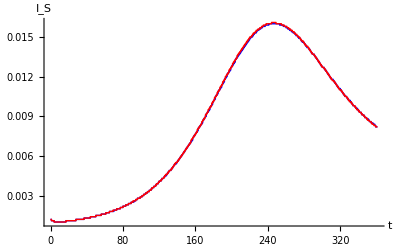
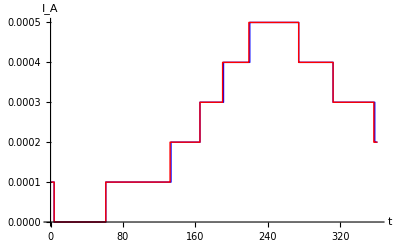
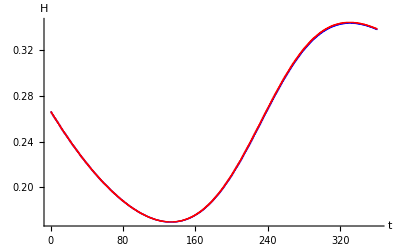
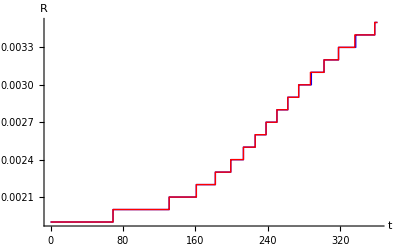

```mathematica
Table[Show[plotdatC[k],plotdatNC[k], PlotRange->All],{k,1,dim-1}]
```